## Stacked disk

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];

Get["TextbookFigurePreamble.wl",Path->FileNameJoin[githubPath,"MathematicalPhyllotaxis\\Mathematica\\Packages"]] 
Get["TextbookStylings.m",Path->FileNameJoin[githubPath,"MathematicalPhyllotaxis\\Mathematica\\Packages"]];
Get["LatticePhyllotaxis`",Path->FileNameJoin[githubPath,"GeometricalPhyllotaxis\\Mathematica\\Packages"]];


Get["DiskStacking`",Path->FileNameJoin[githubPath,"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];


saveRunByTag[run_] :=  Module[{parameters,saveFile,saveRun,tag},
parameters=run["Arena"];
tag=parameters["Tag"];
If[MissingQ[tag],tag="runData"];
saveFile= FileNameJoin[ {runDirectory,tag <> ToString[parameters["Run"]] <> ".mx"}];
saveRun =<|"File"->saveFile,"Run"->run|>;
Export[saveFile,saveRun];
run
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[size_] := Directive[FontFamily->jStyle["FontFamily"],FontSize->size];

leftRightColours=<| RGBColor[1, 0, 0]->jParastichyColour[1],"Left"->jParastichyColour[1],RGBColor[0, 0, 1]->jParastichyColour[2],"Right"->jParastichyColour[2]|>;
```

## Data

## Txb1003InhibitionBoundary

```mathematica
(*notas good *)
showDiskStacking := Module[{},
upto55=Import["upto55.mx",Path->FileNameJoin[githubPath,"MathematicalPhyllotaxis\\Mathematica\\Data"]];
chainLineThickness= AbsoluteThickness[4];
contactLineThickness= AbsoluteThickness[1.5];
pun = DiskStacking`pruneRun[upto55,{14.75,15.7}];
cylinderLU={14.75,15.7}+{0.08,-0.08};
chain=pun["RunChains"][199]["Chain"];
inhibitionNodes=Complement[VertexList[chain],{179,180,183,185,182,187,181,199}];
inhibitionNodes=Join[inhibitionNodes,{right[197]}];
inhibitionDisks=Map[getDiskFromRun[pun,#]&,inhibitionNodes];
nextR= diskR[getDiskFromRun[pun,198]];
centres= Map[DiskStacking`diskXZ[#Disk]&,Values[pun["DiskData"]]];
centres= Select[centres,Last[#]<= diskXZ[getDiskFromRun[pun,199]][[2]]&];
centrePoints= {PointSize[Small],Point[centres,VertexColors->White]};

newDiskZ=diskZ[getDiskFromRun[pun,199]];

Show[
txbExplain[pun,cylinderLU,{"Disks","Centres"},{},199,Missing[]],
Graphics[{
{FaceForm[jParastichyColour[1]],getDiskFromRun[pun,199]},{FaceForm[None],EdgeForm[White],Map[Disk[diskXZ[#],diskR[#]+nextR]&,inhibitionDisks]}
,centrePoints,{Black,InfiniteLine[{0,newDiskZ},{1,0}]}}]
]
];
```

```mathematica
(* better *)olderInhibitionBoundary := Module[{diskSet,disks34 ,disks35,p35,ffs,cylinder,cylinderFrame,g35,grayDisks35,g36,grayDisks36,z35,z36,p36},
diskSet = <|21->Disk[{-0.31713804319567274,6.908413759720007},0.15213435602291286],24->Disk[{-0.17228088512515474,7.158121124069461},0.1365477599015381],22->Disk[{0.05917276231667182,6.996945983663837},0.1454951744167996],25->Disk[{0.2173212678741575,7.223152559389096},0.13051273255583234],23->Disk[{0.4314425128048334,7.057537334974365},0.14018324098016982],26->Disk[{-0.4096117381954028,7.271815971229779},0.12661084643665427],29->Disk[{-0.2271743654346683,7.431101281297408},0.115577520301263],27->Disk[{-0.0007323681160928269,7.353813076343027},0.12369104172621326],30->Disk[{0.17740375194690328,7.511382859721787},0.11413392312215553],28->Disk[{0.38562874656135676,7.407041328312284},0.11877121541941843],31->Disk[{-0.426163668585816,7.53589066661135},0.10931702841669277],34->Disk[{-0.25316045572300766,7.657594990674397},0.10220614798839328],32->Disk[{-0.058791397846309705,7.577953233569368},0.10784656000331899],35->Disk[{0.1008188127986857,7.711935812377165},0.10054430055953617],33->Disk[{0.3621076448232469,7.629897533526779},0.10532280598583793],
36-> Disk[{-0.46682079767965157,7.738451574330346},0.0972838512573701],
37-> Disk[{-0.09613330078020707,7.778037956421985},0.09569290554017923]
|>;
disks34=KeySelect[diskSet,#<=34&];
disks35=KeySelect[diskSet,#<=35&];
p35=First[diskSet[35]];z35=Last[p35];
p36 = First[diskSet[36]];z36=Last[p36];
ffs= Directive[FaceForm[White],EdgeForm[None]];
cylinder = {jStyle["CylinderColour"],Rectangle[{-1/2,0},{7,8.2}]};
cylinderFrame = {FaceForm[None],EdgeForm[LightGray],Rectangle[{-1/2,0},{7,8.2}]};
g35 =Module[{},
grayDisks35 = Block[{xy,r},disks34/. Disk[xy_,r_]-> Disk[xy,r+diskSet[35][[2]]]];
{
cylinder
,{FaceForm[Gray],Map[diskAndVisibleCopies,Values@grayDisks35]}
,{White,Line[{{-1/2,z35},{1/2,z35}}]}
,{PointSize[Medium],jParastichyColour[1],Point[p35]}
,{ffs,Map[diskAndVisibleCopies,Values@disks34]}
, cylinderFrame
}
];
g36 =Module[{},
grayDisks36 = Block[{xy,r},disks35/. Disk[xy_,r_]-> Disk[xy,r+diskSet[36][[2]]]];
{
cylinder
,{FaceForm[Gray],Map[diskAndVisibleCopies,Values@grayDisks36]}
,{White,Line[{{-1/2,z35},{1/2,z35}}]}
,{White,Line[{{-1/2,z36},{1/2,z36}}]}
,{ffs,Map[diskAndVisibleCopies,Values@disks35]}
,{PointSize[Medium],jParastichyColour[1],Point[p35]}
,{PointSize[Medium],jParastichyColour[1],Point[p36]}
, cylinderFrame
}
];
GraphicsRow[{Graphics[g35,PlotRange->{{-1/2,1/2},{7,8.2}},PlotRangeClipping->True],
Graphics[g36,PlotRange->{{-1/2,1/2},{7,8.2}},PlotRangeClipping->True]}]
];
```

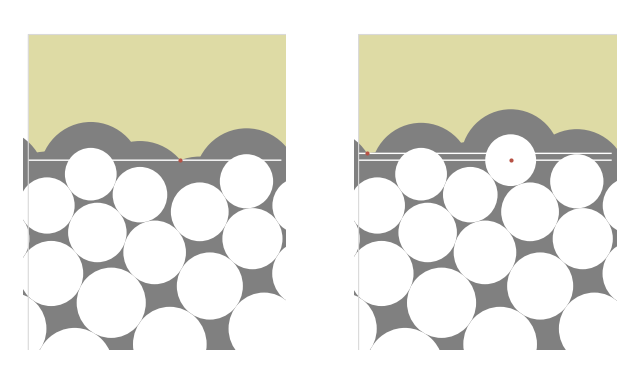

```mathematica
Txb1003InhibitionBoundary  =olderInhibitionBoundary;
txbExport[Txb1003InhibitionBoundary]
```

## Txb1004NonopposedNo

```mathematica
txb10ShowParastichyLines[lattice_,lineColourFunction_]  :=  Module[{ll,llines,paraset,plines,numbers,rise,divergence,glines},
disks= LatticePhyllotaxis`latticeCircles[lattice];
diskAboveCutoff[Circle[{x_,y_},_]]:= y>0.35;
lowerDisks= Select[disks,!diskAboveCutoff[#]&] /. Circle->Disk;
Graphics[{
{jStyle["CylinderColour"],LatticePhyllotaxis`latticeGraphicsCylinder[lattice]}
,{FaceForm[White],lowerDisks}
,{PointSize[Small],Point[LatticePhyllotaxis`latticePoints[lattice]]}
},PlotRange->{{-1/2,.6},{-0.05,0.4}}
,BaseStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.03]]
]
];

txb10NonOpposed := Module[{lattice,dh},
dh=LatticePhyllotaxis`latticeDivergenceRiseForNonOpposedTC[{2,5}];
lattice = LatticePhyllotaxis`latticeFromDivergenceRise[dh, {-0.1,0.5}];

Show[
txb10ShowParastichyLines[lattice,jParastichyColour]
,PlotRange->{{-1/2,1/2},{0,0.6}}
]

];
```

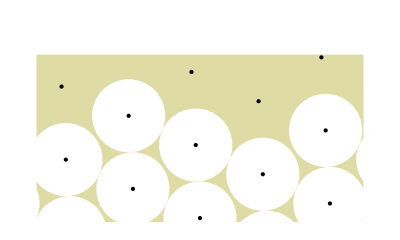

```mathematica
Txb1004NonopposedNo=txb10NonOpposed;
txbExport@Txb1004NonopposedNo
```

## Txb1005DGParastichy

```mathematica
txbExplainParastichy[run_,zRange_,toShow_,mostRecentDisk_] := Module[{chain},
chain=run["RunChains"][mostRecentDisk]["Chain"];
txbExplain[run,zRange,toShow,{mostRecentDisk},mostRecentDisk,chain]
];
```

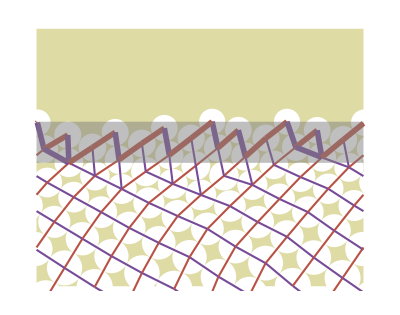

```mathematica
chainLineThickness= AbsoluteThickness[4];
contactLineThickness= AbsoluteThickness[1.5];
upto55= getRunByTag["rcp-upto55-solo1"]["Run"];

pun = DiskStacking`pruneRun[upto55,{14.75,15.7}];
cylinderLU={14.75,15.7}+{0.08,-0.08};
Txb1005DGParastichy = txbExplainParastichy[pun,cylinderLU,{"Disks","Contacts","Centres"},199];
txbExport[Txb1005DGParastichy]
```

## Txb1006DeterministicTransition

### fig : scpDeterministicTransition

```mathematica
chainLines[run_,chainNumber_] := Module[{w},
w=run;
w["ContactGraph"]=run["RunChains"][chainNumber]["Chain"];
graphToContactLines[w,leftRightColours]
];

chainLineThickness= AbsoluteThickness[2];
contactLineThickness= AbsoluteThickness[.5];
```

```mathematica
txbExplain[run_,zRange_,toShow_,chainNumbers_,stackedDiskNumber_,chain_] := Module[{diskNumbers,disks,ffs,cylinder,stackedDisks,stackedRun,nextDisk,contacts,cylinderLU,diskDisks,diskShow,ghainLines,chainBox,g},
ffs= Directive[FaceForm[White],EdgeForm[Black]];
diskNumbers = DiskStacking`diskNumbersInRun[run];
disks =Association@Map[#->DiskStacking`getDiskFromRun[run,#]&,
diskNumbers];
If[MissingQ[stackedDiskNumber],
stackedDisks=disks;stackedRun=run;nextDisk=Nothing[];
,
stackedDisks=KeySelect[disks,#<= stackedDiskNumber&];
stackedRun= DiskStacking`pruneRunByDisks[run,{0,stackedDiskNumber}];
nextDisk =  disks[stackedDiskNumber+1]
];



cylinderLU = zRange;
cylinder = {jStyle["CylinderColour"],Rectangle[{-1/2,cylinderLU[[1]]},{1/2,cylinderLU[[2]]}]};

diskDisks=Map[DiskStacking`diskAndVisibleCopies,Values@stackedDisks];
If[!MemberQ[toShow,"Circles"] || MemberQ[toShow,"Disks"],
diskShow= {}];
If[MemberQ[toShow,"Disks"],
diskShow={Directive[FaceForm[White],EdgeForm[None]],diskDisks}];
If[MemberQ[toShow,"Circles"],
diskShow={Directive[FaceForm[None],EdgeForm[Black]],diskDisks}];
If[MemberQ[toShow,"Circles"] && MemberQ[toShow,"Disks"],
diskShow={Directive[FaceForm[White],EdgeForm[Black]],diskDisks}];

contacts = graphToContactLines[stackedRun,leftRightColours];
ghainLines=Map[chainLines[run,#]&,chainNumbers];

chainBox = If[MissingQ[chain],Nothing[],{FaceForm[{Opacity[0.5],Gray}],EdgeForm[None],chainRectangle[chain]}];

g=Graphics[{
cylinder
,
diskShow
,{
{contactLineThickness,If[MemberQ[toShow,"Contacts"],contacts,Nothing[]]}}
,chainLineThickness,ghainLines
(*,{FaceForm[jParastichyColour[1]],EdgeForm[None],nextDisk}
*),chainBox 
}
,Axes->False,PlotRangeClipping->True
,PlotRange->{{-1/2,1/2},cylinderLU}
]

];
```

```mathematica
graphToContactLines[run_,leftRightColours_] := graphToContactLines[run["ContactGraph"],run,leftRightColours];

graphToContactLines[g_,run_,leftRightColours_] := Module[{dlines,fsort,res},
dlines = Line/@Map[diskXZ[getDiskFromRun[run,#]]&,List@@@EdgeList[g],{2}];fsort[Line[{p1_,p2_}]] := If[First[p1]<First[p2],Line[{p1,p2}],Line[{p2,p1}]];dlines=Map[fsort,dlines];res = lineCylinderIntersectionColoured[#,leftRightColours]& /@dlines;
res
];


lineCylinderIntersectionColoured[Line[{{x1_,z1_},{x2_,z2_}}],leftRightColours_] :=
 Module[{slope,col},
slope= (z2-z1)/(x2-x1);
If[slope>0,col=leftRightColours["Left"],col=leftRightColours["Right"]];If[x1<-1/2,Return[
{col,
Line[{{-1/2, z2 - slope * (x2-(-1/2))},{x2,z2}}], Line[{{x1+1,z1},{1/2,z1+slope *( 1/2-(1+x1))}}]
}
]];
If[x2>1/2,Return[
{col,
Line[{{-1/2, z2- slope * (x2-1-(-1/2))},{x2-1,z2}}], Line[{{x1,z1},{1/2,z1+slope *( 1/2-(x1))}}]
}
]];
Return[{col,Line[{{x1,z1},{x2,z2}}]}] 
];
(*
diskAndVisibleCopies[Disk[{x_,z_},r_]] := {Disk[{x,z},r],If[x+r>1/2,moveDiskLeft[Disk[{x,z},r]],Nothing[]],If[x-r<-1/2,moveDiskRight[Disk[{x,z},r]],Nothing[]]};
*)
```

```mathematica
showZBar=False;

grainLines[run_,col_,zRange_,toShow_,chain_:Missing[],zBarRange_:Missing[]] := Module[{red,g,zTransitionRange,zBar,chainBox,centres,centrePoints},

(*zTransitionRange= Values[KeyTake[run["Arena"],{"rFixedBefore","rFixedAfter"}]];
*)
If[!Missing[zBarRange],
showZBar,zBar= {FaceForm[Gray],EdgeForm[None],Opacity[0.2],Rectangle[{-1/2,zBarRange[[1]]},{1/2,zBarRange[[2]]}]},zBar=Nothing[]];

g=graphToContactLines[run,leftRightColours];
chainBox = If[MissingQ[chain],Nothing[],{FaceForm[{Opacity[0.5],Gray}],EdgeForm[None],chainRectangle[chain]}];
centres= If[MemberQ[toShow,"Centres"],Map[DiskStacking`diskXZ[#Disk]&,Values[run["DiskData"]]],{}];
centrePoints= {PointSize[Small],Point[centres,VertexColors->White]};
centrePoints= Map[Inset[Graphics[{FaceForm[White],EdgeForm[None],Disk[]}],#,Center,0.005]&,centres];
red=Select[g,First[#]==col&];
Graphics[{zBar,contactLineThickness,red,centrePoints,chainBox},Axes->False,PlotRangeClipping->True
,PlotRange->{{-1/2,1/2},zRange}]
]

chainRectangle[chain_] := Rectangle @@{{-1/2,#[[1]]},{1/2,#[[2]]}}&@ MinMax@Map[AnnotationValue[{chain,#},VertexCoordinates][[2]]&,VertexList[chain]];


panelInset[panel_,label_] := Show[panel,Graphics[Inset[Style[label,jFont[Scaled[.1]]],Scaled[{0,1}],Scaled[{0,1}],Background->White]]];
```

```mathematica
chainLineThickness= AbsoluteThickness[4];
contactLineThickness= AbsoluteThickness[1.5];
upto55= getRunByTag["rcp-upto55-solo1"]["Run"];
upto55//Keys
```

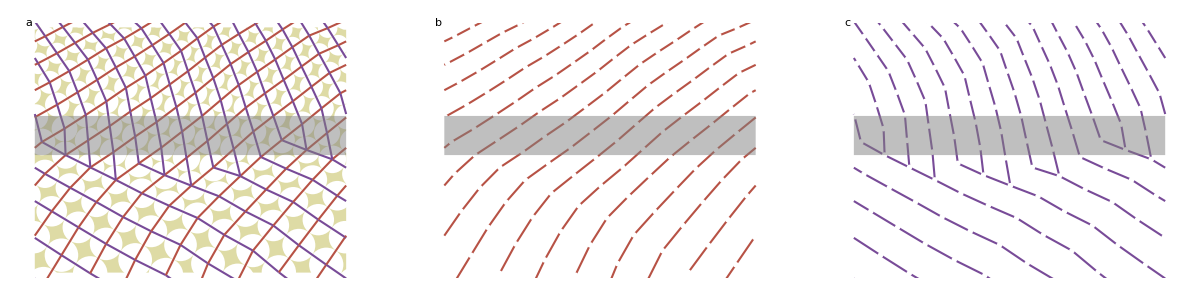

```mathematica
pun = DiskStacking`pruneRun[upto55,{14.75,15.7}];
cylinderLU={14.75,15.7}+{0.08,-0.08};


txbShowGrain[run_,zRange_,toShow_,mostRecentDisk_] := Module[{chain},
chain=run["RunChains"][mostRecentDisk]["Chain"];
GraphicsGrid[{{
panelInset[txbExplain[run,zRange,toShow,{},Missing[],chain],"a"]
,
panelInset[grainLines[run,jParastichyColour[1],zRange,toShow,chain],"b"]
,
panelInset[grainLines[run,jParastichyColour[2],zRange,toShow,chain],"c"]
}}
]
];
txbDeterministicTransition := txbShowGrain[pun,cylinderLU,{"Disks","Contacts","Centres"},199];
Txb1006DeterministicTransition=txbDeterministicTransition;
txbExport@Txb1006DeterministicTransition
```

## Txb1007ParastichyCountsTo89

```mathematica
chainStatistics[run_] := Module[{res,runChains,chainRadii,chainZ},
res=run;
runChains =res["RunChains"];
runChains  = Map[Append[#,<|"DiskNumbers"-> DeleteDuplicates[DiskStacking`bareNumber/@ VertexList[#Chain]]|>]&,runChains];
chainRadii[chain_] := Map[DiskStacking`diskR[res["DiskData"][#]["Disk"]]&,chain["DiskNumbers"]];
chainZ[chain_] := Mean@Map[DiskStacking`diskZ[res["DiskData"][#]["Disk"]]&,chain["DiskNumbers"]];
runChains  = Map[Append[#,<|"MeanZ"-> chainZ[#] |>]&,runChains];
runChains  = Map[Append[#,<|"MeanRadius"-> Mean[chainRadii[#] ]|>]&,runChains];
runChains = Map[KeyDrop[#,"Chain"]&,runChains];
res["RunChains"]=runChains;
res
];

chainToPoints[chain_] :={ {leftRightColours[RGBColor[1, 0, 0]],Point[{1/chain["MeanRadius"],chain["Parastichy"][RGBColor[1, 0, 0]]}]}
,{leftRightColours[RGBColor[0, 0, 1]],Point[{1/chain["MeanRadius"],chain["Parastichy"][RGBColor[0, 0, 1]]}]}
};

fRange=Table[Fibonacci[n],{n,7,11}];

showParaTransitions[oChains_] := Module[{},
Legended[Graphics[
{PointSize[Small],Map[chainToPoints,Values[oChains]]
},
Ticks->{Automatic,Prepend[Table[Fibonacci[n],{n,7,11}],1]},
GridLines->{fTransitions,None},
AxesLabel->{"Radius^-1","Parastichy"},AxesStyle->{jFont[12],jFont[12]},
Axes->True,BaseStyle->jFont[12]
],Placed
[SwatchLegend[Directive[EdgeForm[None],FaceForm[leftRightColours[#]]]&/@{RGBColor[1, 0, 0],RGBColor[0, 0, 1]},{"Left parastichy count","Right parastichy count"},
LabelStyle->jFont[12],
LegendFunction-> (Framed[#,Background->White,FrameStyle->None]&)
],{0.25,0.8}]
]
];

fTransitions= Map [   2Sqrt[2]#&,fRange];
```

```mathematica
upto89=getRunByTag["rcp-upto89-solo1"]["Run"];
upto89RunChains = chainStatistics[upto89]["RunChains"];
```

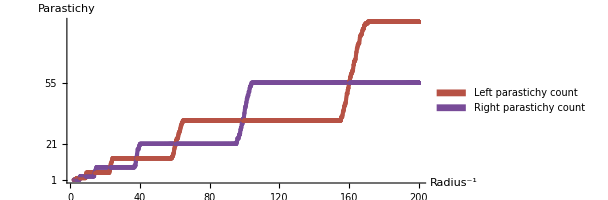

```mathematica
Txb1007ParastichyCountsTo89 = showParaTransitions[upto89RunChains];
txbExport[Txb1007ParastichyCountsTo89]
```

## Run execution code

```mathematica
latestRadius[run_] := Last@Values[DiskStacking`runDisksRadius[run]];
latestCentre[run_] := Last@Values[DiskStacking`runDisksHeight[run]];

readyRunFromParameter[lastRun_,experimentParameters_] := Module[{runParameters,run,arena,initialRadius,finalRadius,initialZ,makef,finalZ,showArena},

(* set defaults *)
runParameters= <|
"rScale"->10,
"rSlope"->0.03,
"power"-> 1,
"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1}],
"zMax"->Missing[],
"runNumber"->1,
"diskMax"->∞,
"PostFixChains"->0,
"Run"->"",
"Noise"->Missing[]
|>;

runParameters= Append[runParameters,experimentParameters];
run=lastRun;

If[!KeyMemberQ[experimentParameters,"radiusFunctionParameters"],
run["Arena"] = createArena[run,runParameters]
,
run["Arena"] = createRFunctionArena[{latestCentre[run],latestRadius[run]},runParameters]
];
;
run
];


createRFunctionArena[{initialZ_ ,initialRadius_},runParameters_] := Module[{arena,sectionStartRadius,sectionStartZ,functionCount,rFunctionPieces},

calcfunctionParameters[functionParameter_] := Switch[functionParameter["Type"],
"Constant",constFunctionParameters[functionParameter]
,
"LinearReduction",linearFunctionParameters[functionParameter]
,
"LinearCircumferenceIncrease",inverseLinearDecreaseFunctionParameters[functionParameter]
,
_,
 Print["Type not set ",functionParameter];Abort[];
];
inverseLinearDecreaseFunctionParameters[functionParameter_] := Module[{res,circumferenceStart,circumferenceScale,rStart,circumferenceEnd,rEnd,zEnd,func},
circumferenceStart = 1/sectionStartRadius;
circumferenceEnd = circumferenceStart* functionParameter["circumferenceScale"];
zEnd = sectionStartZ+functionParameter["zRange"];
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius
,"rEnd"->  sectionStartRadius/functionParameter["circumferenceScale"]
,"rScale"-> 1/functionParameter["circumferenceScale"]
,"zStart"-> sectionStartZ
,"zEnd"-> zEnd|>
];
func = Function[{z},sectionStartRadius*(zEnd-sectionStartZ) / (-(z-zEnd) +(functionParameter["circumferenceScale"])*( z-sectionStartZ))];
res["rFunction"] = functionClosure[func];

sectionStartZ = res["zEnd"];
sectionStartRadius = res["rEnd"];
res
];
linearFunctionParameters[functionParameter_] := Module[{res,rStart,rEnd},
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius,
"rEnd"-> sectionStartRadius/functionParameter["rScale"]
,"zStart"-> sectionStartZ|>
];
res = Append[res,linearFunctionProperties[ {res["rStart"],res["rEnd"]},res["rSlope"],sectionStartZ]];
sectionStartZ = res["zEnd"];
sectionStartRadius = res["rEnd"];
res
];
constFunctionParameters[functionParameter_] := Module[{res,finalRadius},
res = Append[functionParameter,
<|"rStart"-> sectionStartRadius
,"rEnd"-> sectionStartRadius
,"zStart"-> sectionStartZ
,"zEnd"-> sectionStartZ + functionParameter["ApproximateChains"]* 4* sectionStartRadius
|>];
res = Append[res,<|"rFunction"->Function[{z},Evaluate[sectionStartRadius]]|>];
sectionStartZ = res["zEnd"];
res
];
functionListToPieceWise[flist_] := Module[{piece,pieceFunction},
piece [z_] := KeyValueMap[{(lookup[#1]),#2["zStart"]<z< #2["zEnd"]}&,flist];
pieceFunction[z_] := Evaluate[Piecewise[piece[zq]] /. zq->z];
pieceFunction
];


sectionStartZ =  initialZ;
sectionStartRadius = initialRadius;
functionCount = 1;

arena = runParameters;
arena["rFunctionList"] = Association@Map[functionCount++->calcfunctionParameters[#]&,arena["radiusFunctionParameters"]];

bq=KeyValueMap[{(lookup[#1]),#2["zStart"]<z<= #2["zEnd"]}&,arena["rFunctionList"]];
bq = Prepend[bq,{arena["rFunctionList"][1]["rStart"],z<= arena["rFunctionList"][1]["zStart"]}];
bq = Append[bq,{Last[arena["rFunctionList"]]["rEnd"],z > (Last[arena["rFunctionList"]])["zEnd"]}];

rFunctionPieces = bq  /. lookup[i_] :> arena["rFunctionList"][i]["rFunction"][z];

arena["rFunctionPieces"] = rFunctionPieces ;
arena["rFunction"] := Function[{zq},Piecewise[arena["rFunctionPieces"]]/. z-> zq]; 
arena["zMax"] = (Last[arena["rFunctionList"]])["zEnd"]; 
arena

];






createArena[run_,runParameters_] := Module[{arena,initialRadius,finalRadius,initialZ,makef,finalZ,showArena},

(* create the r Function *)
initialRadius=latestRadius[run];
initialZ =  latestCentre[run];
finalRadius= initialRadius/runParameters["rScale"];

makef=powerFunctionProperties[ {initialRadius,finalRadius},runParameters["rSlope"],initialZ,
runParameters["power"]];
finalZ = makef["zEnd"];

arena=KeyDrop[runParameters,{"Lattice"}];
arena["rFunction"]= makef["Function"];
arena["zMax"]= finalZ + runParameters["PostFixChains"]* 4* finalRadius;
arena
];


linearFunctionProperties[ {rStart_,rEnd_},rSlope_,zStart_,power_:1] := Module[{zSlopeRange,zEnd,func,rDash,scaler},
rDash = -rSlope;
scaler = Sign[rDash]*(Abs[(zEnd-zStart) * rDash] )^ (power-1);
zEnd = zStart + ( (rEnd-rStart))/rDash ;

func = Function[{z},rStart+(((z-zStart) * Abs[rDash])^power)/scaler];
func  = functionClosure[func];
<|"rFunction"-> func, "zEnd"-> zEnd|>
]

powerFunctionProperties[ {rStart_,rEnd_},rSlope_,zStart_,power_] := Module[{zSlopeRange,zEnd,f,rDash,scaler},
rDash = -rSlope;
scaler = Sign[rDash]*(Abs[(zEnd-zStart) * rDash] )^ (power-1);
zEnd = zStart + ( (rEnd-rStart))/rDash ;

f = Function[{z}, rStart+ Piecewise[ {
{0,z< zStart}
,{(((z-zStart) * Abs[rDash])^power)/scaler, z< zEnd}
, { (((zEnd-zStart) *Abs[ rDash] ))^power/scaler,True}
}]];
f = functionClosure[f];
<|"Function"-> f, "zEnd"-> zEnd|>
]

functionClosure[f_] := Function[{z$},Evaluate[f[[2]]]]
```

```mathematica
doOneRun[parameters_] := Module[{run},
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run=doMonitoredRun[run];
saveRunByTag[run];
run
];
doMonitoredRun[run_] := Module[{res},
SeedRandom[run["Arena"]["Run"]];
res=run;
monitorRun= res["Arena"]["Run"];
monitorPP = <|"Noise"->res["Arena"]["Noise"],"rSlope"->res["Arena"]["rSlope"]|>;
res = DiskStacking`executeRun[res]; 
res 
];

retrieveRFunction[savedRun_] := Module[{run,parameters},
parameters=savedRun["Arena"];
run = DiskStacking`runFromLattice[parameters["Lattice"]];
run= readyRunFromParameter[run,parameters] ; 
run["Arena"]["rFunction"]
];

restartOneRun[lastRun_] := Module[{run},
run=lastRun;
run = DiskStacking`restartRunFromRun[run];
run= readyRunFromParameter[run,lastRun["Arena"]] ; 
run=doMonitoredRun[run];
saveRunByTag[run];
run
]
doRunSets[parameterSets_] := Module[{res,abortCheck,runSets,timing},
abortCheck[parameterSet_] := CheckAbort[doOneRun[parameterSet],Print["Abort running ",parameterSet["Run"]]; Missing[parameterSet["Run"]]];
monitorRunTotal = Length[parameterSets];
monitorRunNumber= 0;
{timing,res}= Timing[Monitor[runSets=Map[(monitorRunNumber++;abortCheck[#]&),parameterSets],{monitorRunTotal,monitorRunNumber,monitorRun,monitorPP}];];
runSets
];

expandParameterSets[parameterListAssociation_] := Module[{res,runCount=1,parameterNames,parameterLists,labelParameter},
parameterNames= Keys[parameterListAssociation];
parameterLists = Values[parameterListAssociation];
labelParameter[parameterList___] := Append[Association@Thread[parameterNames ->{parameterList}],"Run"->runCount++];
res=Flatten[Outer@@ Prepend[parameterLists,labelParameter]]
];
```

## Txb1008FixedRadius

```mathematica
doFixedRadiusDynamics [jiggles_]:= Module[{},
arena2= <|"runNumber"->1
,"Tag"->"test-constant"
,"Run"->""
,"radiusFunctionParameters" -> {
<|"Type"->"Constant","ApproximateChains"->1|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{5,8},cylinderLU={-0.01,2}]
|>;
run23 = doOneRun[arena2];
restart23 =run23;
globalLastDiskNumber=Max[Keys@restart23["DiskData"]];

restart23["Arena"]["zMax"]=6;
jiggleLastDiskOfRun[run_,jiggle_] := Module[{res=run,lastDiskNumber,disk},
lastDiskNumber=Max[Keys@res["DiskData"]];
disk = res["DiskData"][lastDiskNumber]["Disk"];
disk = Disk[diskXZ[disk],jiggle * diskR[disk]];
res["DiskData"][lastDiskNumber]["Disk"] = disk;
res 
];

restart23Set=Map[jiggleLastDiskOfRun[restart23,#]&,jiggles];
resultSet=Map[DiskStacking`executeRun[#]&,restart23Set];
resultSet
];

showFixedRadiusDynamics [lastDiskNumber_,resultSet_] := Module[{},
GraphicsRow[Map[
Show[
txbExplain[#,{2,6},{"Disks","Contacts"},{},Missing[],Missing[]]
,
Graphics[
{Opacity[0.5],FaceForm[jParastichyColour[1]]
,#["DiskData"][lastDiskNumber]["Disk"]
}]]&,resultSet]
]
]
```

```mathematica
rebuildingData=False;
If[rebuildingData,
resultSet=doFixedRadiusDynamics [{0.6,0.8,1,1/0.8,1/0.6}];
Export["Txb1008DataJiggle.mx",resultSet],
resultSet=Import[FileNameJoin[githubPath,"MathematicalPhyllotaxis\\Mathematica\\Data\\Txb1008DataJiggle.mx"]]
];
```

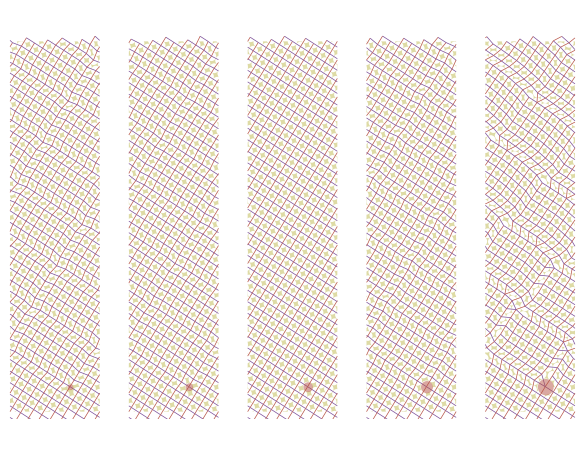

```mathematica
Txb1008FixedRadius = showFixedRadiusDynamics [globalLastDiskNumber=202,resultSet];
txbExport[Txb1008FixedRadius]
```

## Txb1009AreaTimeSeries

0

```mathematica
tripleGraph[g_] := Module[{},
nodes=Select[VertexList[g],NumberQ[#]&];
edges=EdgeList[g]/. {Private`left->left,Private`right->right};
moveEdgeLeft[a_<->b_] := left[a]<->left[b];
moveEdgeRight[a_<->b_] := right[a]<->right[b];
leftEdges= moveEdgeLeft/@edges   /. {left[right[x_]]:> x,right[left[x_]]:> x};
rightEdges= moveEdgeRight/@edges   /. {left[right[x_]]:> x,right[left[x_]]:> x};
gLR=Graph[Map[Tooltip[#,#]&,nodes],Join[edges,leftEdges,rightEdges]];
gLR= VertexDelete[gLR,Select[VertexList[gLR],( MatchQ[#,left[left[_]]] | MatchQ[#,right[right[_]]])&]];
vxy[x_?NumberQ] := AnnotationValue[{g,x},VertexCoordinates];
vxy[left[x_]] := vxy[x]-{1,0};
vxy[right[x_]] := vxy[x]+{1,0};
gLR=Graph[gLR,VertexCoordinates->Map[#->vxy[#]&,VertexList[gLR]]];
gLR= Graph[gLR,VertexSize->Medium]
];

polygonBelow[g_,v_] := Module[{gBelow},
vDelete=Select[VertexList[g],AnnotationValue[{g,#},VertexCoordinates][[2]]>AnnotationValue[{g,v},VertexCoordinates][[2]]&];
gBelow=VertexDelete[g,vDelete];
cycles=FindCycle[{gBelow,v},{3,5},∞];
cycles=SortBy[cycles,Length];
If[Length[cycles]==0,Return[Missing[]]];
polygon=First/@ First[cycles];
Polygon[Map[AnnotationValue[{g,#},VertexCoordinates]&,polygon]]
];

graphPolygons[g_] := Module[{g3,nodes},
g3=tripleGraph[g];
nodes=Select[VertexList[g],NumberQ];
Association@Map[#->polygonBelow[g3,#]&,nodes]
];

graphNodeArea[g_] := Module[{polys},
polys=graphPolygons[g];
Map[If[MissingQ[#],#,Area[#]]&,polys]
];
```

```mathematica
areaStatistics[result_] := Module[{graphPolygons,polygons},
graphNodeArea[result["ContactGraph"]]
];
```

```mathematica
showAreaResultset[areasByRun_] :=Module[{sf},
dff=Directive[FontFamily->jStyle["FontFamily"]];
aByRun=Map[DeleteMissing,areasByRun];
sf=First@aByRun[[1]];
l1=aByRun[[1]]/sf;
l2=aByRun[[2]]/sf;
l3=aByRun[[3]]/sf;
ListPlot[{Labeled[l1,Style["a",dff]],Labeled[l3,Style["c",dff]]}
,PlotRange->{{199,543},{0.4,1.2}}
,PlotLegends->{"a","c"}
,AxesLabel->{"Node number","Relative area"}
 ,PlotStyle->PointSize[.01]
,AxesStyle->dff,LabelStyle->dff
,Frame->True,FrameLabel->{{"a"},"b"}
,PlotLayout->"Row",
Method->{"Spacings"->{5,5},"ColumnLabels"->{{"bottom left","top left"},{"bottom right","top right"}},"RowLabels"->{{"left top","right top"},{"left bottom","right bottom"}}}
]
];
```

```mathematica
areasByRun = Map[areaStatistics,resultSet];
```

```mathematica
Txb1009AreaTimeSeries =showAreaResultset[areasByRun];
txbExport[Txb1009AreaTimeSeries]
```

-Graphics-

## Txb1010Tilings

```mathematica
centralPolygons[theta_] :=  Module[{},
(* between 60 and 120 *)
phi=(theta -60 Degree )/2;
rhomboidR=1/(4 Cos[phi]);
(*phi=15 Degree -(theta -60 Degree )/2; 
*) (* nb with a different format would for theta>90  ... *) 
secondaryParastichy= {Cos[theta],Sin[theta]};
p11= 2* rhomboidR* {Cos[theta+phi],Sin[theta+phi]};
p01= 2* rhomboidR* {Cos[phi],Sin[phi]}; (*= {1/2,2 r Sin phi *) 
points=<|"P00"->{0,0},"P10"->p01,"P20"->{1,0},"P01"-> p11,"P11"->p11+p01,"P21"->{1,0}+p11,
"P02"->secondaryParastichy,"P12"->secondaryParastichy+p01,"P22"->secondaryParastichy+{1,0}|>;
polygons= <|
"Poly00"->Polygon[{points["P00"],points["P10"],points["P11"],points["P01"]}]
,"Poly10"->Polygon[{points["P10"],points["P20"],points["P21"],points["P11"]}]
,"Poly01"->Polygon[{points["P01"],points["P11"],points["P12"],points["P02"]}]
,"Poly11"->Polygon[{points["P11"],points["P21"],points["P22"],points["P12"]}]

|>
];
latticeUnit[lattice_]:= Module[{},
p1=lattice["parastichyVectors"][[1]];
p2=lattice["parastichyVectors"][[2]];
internalAngle= ArcCos[(p1.p2)/(Norm[p1]*Norm[p2])];
p1Rotation = ArcTan@@ p1;
polys=centralPolygons[5π/12];
swatch=<|"Poly00"->jParastichyColour[1],"Poly10"->jParastichyColour[2],"Poly01"->jParastichyColour[3],"Poly11"->jParastichyColour[4]|>;
polys= KeyValueMap[{swatch[#1],GeometricTransformation[#2,RotationTransform[p1Rotation]@*ScalingTransform[{Norm[p1],Norm[p1]}]]}&,centralPolygons[5π/12]];
polys
];

multiUnits[lattice_,pRange_] := Module[{unit},
unit=latticeUnit[lattice];
pointNumbers=Range@@pRange;
points= N@latticePoint[lattice,#]&/@pointNumbers;
points=Join[points, Map[#+{1,0}&,points], Map[#-{1,0}&,points]];
GeometricTransformation[unit,Map[TranslationTransform,points]]
]
```

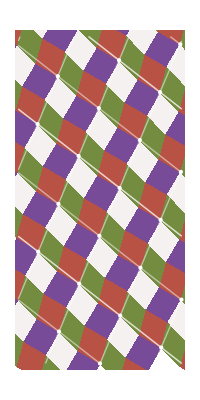

```mathematica
lattice= latticeCreateDH[
Simplify[latticeMoebiusTransform[{2,3}][ {Cos[7π/12],Sin[7π/12]}]],{0,2},2];
showRhomboids := Graphics[{
multiUnits[lattice,{-3,20}],
{Opacity[0.5],White,latticeParastichyLines[lattice,2],latticeParastichyLines[lattice,3]}
,
{White,PointSize[Small],latticeGraphicPoints[lattice]}
},PlotRange->{{-1/2,1/2},{0,2}},PlotRangeClipping->True];
Txb1010Tilings=showRhomboids;
txbExport[Txb1010Tilings]
```

## Txb1012TransitionLattices

```mathematica
fType[x_] := Which[
MemberQ[{13,21,34,55,89,144}-1,x],"Fibonacci ±1",
MemberQ[{13,21,34,55,89,144}+1,x],"Fibonacci ±1",
MemberQ[{1,4,5,9,14,23,37,60,97},x],"F4",
MemberQ[{1,3,4,7,11,18,29,47,76,123},x],"Lucas",
MemberQ[{2,4,6,10,16,26,42,68,110},x],"Fibonacci x2",
MemberQ[{1,2,3,5,8,13,21,34,55,89,144},x],"Fibonacci",
True,"Other"
];

histobars[counts_] := KeyValueMap[{grainCountStyling[#1],Rectangle[{#1-0.4,0},{#1+0.4,#2}]}&,counts/Total[counts]];
paraScaling[x_] := Log10[1+x];
paraScaling[x_] := x;
textSize = jFont[9];
clabel[run_] := StringTemplate["r':`rSlope` σ: `Noise`"][run["Arena"]]

grainCountStyling[count_] := txbPalette[fType[count]];

txbPalette = <|
"Fibonacci"->Directive[FaceForm[None],EdgeForm[jStyle["ParastichyColour"][1]]]
,"Fibonacci x2"-> jStyle["ParastichyColour"][2]
,"Lucas"-> jStyle["ParastichyColour"][3]
,"F4" -> Directive[FaceForm[ jStyle["ParastichyColour"][4]],EdgeForm[{Black}]]
,"Fibonacci ±1"-> jStyle["ParastichyColour"][5]
,"Other"-> jStyle["CylinderColour"]
|>;
parastichyCounts[run_,col_] := Module[{paras,counts,clook},
paras=Map[#Parastichy&,run["RunChains"]];
If[col==={RGBColor[0, 0, 1],RGBColor[1, 0, 0]},
counts= Flatten@Values[Values /@ paras];
counts= Counts[counts]
,
clook= If[col==RGBColor[0, 0, 1],clook=RGBColor[1, 0, 0],clook=RGBColor[0, 0, 1]];
counts =Counts[Map[#[clook]&,paras]]
];
counts=paraScaling/@counts;
counts 
];
parastichyBars[run_,col_] := Module[{counts,bars},
counts =parastichyCounts[run,col]; 
bars= histobars[counts];
bars
]
parastichyBarGraph[run_,hRange_,col_] := Module[{g,axis},
If[Length[col]==0,
g={};axis=Transparent
,
g=parastichyBars[run,col];axis=Black];
Graphics[g,Axes->{True,False}
,AxesStyle->axis
,PlotRange->{hRange,{0,paraScaling[1]}},AspectRatio->1,
Ticks->{{5,8,13,21},{None}},
BaseStyle->textSize]
];

pcolumn[run_,hRange_,zRange_,col_] := GraphicsColumn[{
 parastichyBarGraph[run,hRange,col],
grainLines[run,leftRightColours[col],zRange,{}]
},Frame->None];

grainColShow[run_,hRange_,zRange_] := 
GraphicsRow[
{pcolumn[run,hRange,zRange,RGBColor[0, 0, 1]],pcolumn[run,hRange,zRange,RGBColor[1, 0, 0]]
,qcolumn[run,hRange,zRange,Missing[]]},Frame->None];

qcolumn[run_,hRange_,zRange_,dRange_] := Module[{r},
If[MissingQ[dRange],r={},r=Rectangle[{dRange[[1]],zRange[[1]]},{dRange[[2]],zRange[[2]]}]];
GraphicsColumn[{
 parastichyBarGraph[run,hRange,{RGBColor[0, 0, 1],RGBColor[1, 0, 0]}],
Show[txbExplain[run,{0,2},{"Disks","Contacts"},{},Missing[],Missing[]]
,Graphics[{FaceForm[Opacity[0.1],Gray],r}]]
},Frame->None]
];
zColumn[run_,hRange_,zRange_,dRange_] := GraphicsColumn[{
 parastichyBarGraph[run,hRange,{}],
Show[txbExplain[run,{0,2},{"Disks","Contacts"},{},Missing[],Missing[]],
PlotRange->{dRange,zRange}]
},Frame->None];
```

```mathematica
runQSS= getRunByTag["rcp-QSS1"]["Run"];
txbColumn = grainColShow[runQSS,{12,22},{0,2}];
Txb1012TransitionLattices= txbColumn;
txbExport[Txb1012TransitionLattices]
```

-Graphics-

## Txb1013AhaPair

```mathematica
histogramOverRun[run_] :=Module[{counts},
counts =Flatten[Values/@Values[run["ChainParastichies"]]];
counts= Flatten@ Normal[counts];
counts=GroupBy[counts, First->Last ,Total];
counts
];
histogramOverRuns[runList_] := Module[{counts},

counts=Map[histogramOverRun,runList];
counts =Flatten[Normal/@counts];
counts=GroupBy[counts, First->Last ,Total];
counts 
];
paraScaling[x_] := Log10[1+x];
paraScaling[x_] := x;
paraScaling[x_] := Log10[1+x];


countStyling[count_] := txbPalette[fType[count]];

histogramBars[runList_] :=  Module[{counts,bars},
If[MissingQ[runList],Return[{}]];
counts=histogramOverRuns[runList];
counts = N@ counts/Total[counts];
counts = paraScaling/@counts;
bars=KeyValueMap[{countStyling[#],Rectangle[{#1-0.4,0},{#1+0.4,#2}]}&,counts]
];
histogram[runList_] :=  Module[{counts},
Graphics[{jParastichyColour[1]
,histogramBars[runList]}
,PlotRange->{{12,56},{0,0.07}}
,PlotRangeClipping->True
,PlotRangePadding->None
,Ticks->{{13,21,34,55},None}
,BaseStyle->jFont[10]
,Axes->{True,False}
,AspectRatio->1
,Background->Lighter[Gray, 0.9]
]

];
legend =SwatchLegend[Values[txbPalette],Keys[txbPalette],LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.02]]];

bar[{spirals_,observed_}] := Module[{barColour},
barColour = txbPalette[fType[spirals]];
{barColour,Rectangle[ {spirals-0.45,0},{spirals+0.45,observed}]}
];
frame ={{True,True},{True,True}};
countMOSI = {89,89,89,89,89,55,74,89,55,89,53,54,34,89,55,55,34,55,21,55,34,41,55,88,36,29,42,21,18,34,55,89,55,89,55,89,76,89,83,55,55,55,78,55,88,89,89,144,89,89,93,55,89,89,88,55,89,89,68,89,89,34,55,89,76,34,54,89,144,55,55,88,55,89,73,89,68,89,88,86,90,143,110,89,143,142,144,144,89,89,89,89,34,21,79,55,88,34,54,47,48,50,89,54,89,59,55,68,55,55,55,76,89,55,55,47,89,55,89,33,35,43,57,20,19,55,40,89,89,47,55,34,53,84,89,89,89,89,55,34,34,34,54,55,55,55,55,89,89,55,55,55,55,55,55,55,87,123,33,55,89,55,55,143,89,55,53,89,89,76,54,21,33,47,32,55,49,89,76,55,55,89,68,55,89,34,55,56,57,89,53,89,55,88,55,55,55,55,55,34,55,55,55,55,34,34,55,144,76,34,55,89,55,89,34,55,55,55,76,144,19,57,21,34,55,89,89,68,89,89,55,89,88,89,88,50,89,89,89,55,75,88,55,34,89,89,54,89,89,89,89,55,55,55,55,34,34,144,54,89,88,55,55,89,89,55,89,55,55,55,86,89,54,86,89,55,73,89,80,34,55,89,34,89,53,89,55,89,89,55,34,55,34,55,55,55,68,89,55,34,89,55,68,77,47,55,55,55,55,55,54,47,89,55,34,54,55,88,34,55,47,55,55,34,55,55,55,55,55,74,89,54,89,55,55,55,55,55,55,55,55,42,55,54,55,55,68,55,55,55,54,55,55,55,47,55,55,55,55,68,55,55,55,47,55,55,88,50,89,112,89,89,89,89,89,55,68,55,55,55,55,55,55,62,44,29,55,89,89,55,55,34,55,34,34,34,89,75,87,52,55,55,55,56,55,34,55,34,53,34,36,21,55,34,21,34,20,34,21,25,34,55,21,20,26,13,21,34,55,36,55,34,55,47,55,49,35,34,47,34,55,55,89,55,57,34,55,55,55,34,55,55,42,55,55,22,34,55,47,21,34,55,89,34,34,55,34,55,45,55,42,55,54,54,89,68,55,90,89,89,89,55,55,55,55,21,47,55,21,34,29,48,55,55,55,42,34,34,34,47,55,34,34,29,55,34,55,21,21,29,33,13,34,55,55,28,34,34,54,55,55,55,55,34,21,21,21,34,34,34,34,55,54,34,34,34,34,34,34,55,76,19,35,55,34,34,88,55,34,35,55,55,47,36,13,21,29,34,32,56,47,36,34,55,42,34,55,21,34,54,56,34,55,34,34,34,34,34,21,34,34,34,34,21,21,34,47,21,34,55,34,55,34,34,34,47,89,18,34,13,21,34,55,55,42,55,55,34,54,55,55,55,55,55,55,34,48,34,21,55,56,35,55,55,55,55,34,34,36,34,21,21,89,34,55,55,34,34,55,55,55,34,34,34,56,54,34,55,56,34,55,55,68,21,34,55,21,55,34,55,55,34,21,34,34,34,34,42,54,34,21,54,34,56,29,34,34,34,34,34,34,29,55,34,21,34,34,55,21,34,29,34,34,34,34,34,34,34,46,55,34,55,36,35,38,37,34,34,34,34,27,34,34,34,33,42,34,34,34,34,34,34,34,29,34,34,34,34,42,34,36,34,29,34,34,55,31,55,69,55,55,55,55,55,34,42,34,34,34,34,34,34,31,28,34,54,55,34,34,21,34,21,21,21,55,47,52,31};
```

```mathematica
groupedupto55Results=Import[FileNameJoin[{eSetDirectory,"rcp-esetupto55-wxy.mx"}]];
upto55Show = KeySelect[groupedupto55Results,#rSlope< 0.15&];
ahaRun= upto55Show[<|"rSlope"->0.03,"Noise"->0.05|>] ;
(*txbAha = Legended[
Show[histogram[ahaRun],Axes->{True,True},PlotRange->{{10,55},{0,0.04}},FrameLabel->{"Parastichy number","Frequency"},Frame->True,FrameTicks->{Automatic,Automatic},Background->None]
,Placed[legend,Right]]*)
xRange={19.5,57.5};
g2 = Graphics[
{Map[bar,Tally[countMOSI]]},
Axes->True,
AxesOrigin->{20,0},AspectRatio->1,PlotRangeClipping->True,
FrameLabel->{"Parastichy number","Observed"},Frame->frame,
BaseStyle->jFont[12],
PlotRange->{xRange,{0,25}}];
txbAhaPair = Legended[GraphicsRow[{g2,
Show[histogram[ahaRun],Axes->{True,True},PlotRange->{xRange,{0,0.02}},FrameLabel->{"Parastichy number","Simulated"},Frame->True,
BaseStyle->jFont[12],Background->None]
}],Placed[legend,Right]];
```

```mathematica
Txb1013AhaPair=txbAhaPair;
```

```mathematica
txbExport[Txb1013AhaPair];
```

## Txb1014ConeTransformation

```mathematica
arena1014= <|"runNumber"->1
,"Tag"->"txb-radius-34bis-crecrease"
,"Run"->""
,"radiusFunctionParameters" -> {
<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"->1.7,
"zRange"-> 0.1|>
,<|"Type"->"Constant","ApproximateChains"->1|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.9,"zRange"->0.02|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.4/0.9,"zRange"->0.15|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.2/(0.4/0.9),"zRange"->0.15|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{21,34},cylinderLU={-0.01,0.1}]
|>;
rebuildingData=False;
If[TrueQ[rebuildingData],
runCone2  = doOneRun[arena1014];
saveRunByTag[runCone2];
,
runCone2=getRunByTag["txb-radius-34bis-crecrease"]["Run"]
];
```

```mathematica
maketxbConeTransformation :=Module[{},
runCone= getRunByTag["txb-radius-34bis-crecrease"]["Run"];
stemParameters = runCone["Arena"]["rFunctionList"] ;
stemParameters = KeyMap[<|1->"cone",2->"bract",3->"ray",4->"seed",5->"inner"|>[#]&,stemParameters];
diskRun = DiskStacking`pruneRun[runCone,{stemParameters["bract"]["zStart"],stemParameters["inner"]["zEnd"]}];
diskShow :=makeDiskGraphics[diskRun];
cylinderRun = DiskStacking`pruneRun[runCone,{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}];
cylinderShow = makeCylinderGraphics[cylinderRun];
 GraphicsColumn[{cylinderShow,diskShow},Frame->False]
];
Txb1014ConeTransformation=maketxbConeTransformation;
```

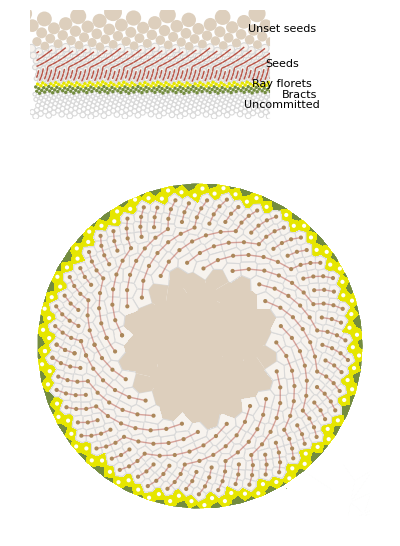

```mathematica
txbExport@Txb1014ConeTransformation
```

```mathematica
makeCylinderGraphics[run_] := Module[{namedPoints,namedType,colouredNodes,namedDisks,colouredDisks,textOffset,partLabels,partText,cropRectangle,seedRun,seedParastichyLeft},
namedPoints = Point /@ runTransformedNodes[run,Identity,bareOnly=True];
namedType = nodeType /@  runTransformedNodes[run,Identity];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
namedDisks = runDisks[run];
colouredDisks= Association@Map[#->{
FaceForm[cylinderDiskColour[namedType[#]]]
,EdgeForm[cylinderDiskBoundaryColour[namedType[#]]]
,namedDisks[#]}&,Keys[namedDisks]];
textOffset[type_] := If[type==="bract",{-1,.75},{-1,0}];
partLabels =<|"cone"->"Uncommitted","bract"->"Bracts","ray"->"Ray florets","seed"-> "Seeds","inner"->"Unset seeds"|>;
partText =Style[KeyValueMap[Text[partLabels[#1],{0.55,Mean[{#2["zStart"],#2["zEnd"]}]},textOffset[#1]]&,stemParameters],jFont[12]];
cropRectangle = {FaceForm[White],EdgeForm[None],Rectangle[{1/2,-1},{2,10}]};
seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];
seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];

Graphics[{Values@colouredDisks,seedParastichyLeft,cropRectangle,partText},PlotRange->{{-1/2,.9},{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}}]
];
```

```mathematica
diskTransform[{zMin_,zMax_}] := Module[{f},
f= Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = zMax- z;
r= r/(zMax-zMin); (* outer ring radius 1 *)
r*{Cos[2 π x],Sin [ 2 π x]} 
]
];
f
];
```

```mathematica
makeDiskGraphics[run_] :=Module[{runDiskTransform,namedPolygons,namedType,namedPoints,colouredNodes,cropDisk,colouredPolygons,namedDiskNodes,seedRun,seedParastichyLeft,seedDiskParastichy,lColour,plotRange,diskShow},
runDiskTransform := diskTransform[{stemParameters["ray"]["zStart"],stemParameters["inner"]["zEnd"]}];
namedDiskNodes = runTransformedNodes[run,runDiskTransform] ;
namedPolygons = namedPointsToVoronoiPolygons[namedDiskNodes];

namedType = nodeType /@  runTransformedNodes[run,Identity];
namedPoints = Point /@ runTransformedNodes[run,runDiskTransform];
colouredNodes= Association@Map[#->{nodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];

cropDisk = {FaceForm[White],EdgeForm[White],MeshPrimitives[DiscretizeRegion[RegionDifference[Rectangle[1.2*{-1,-1},1.2*{1,1}],Disk[{0,0},1.02]]],2]};colouredPolygons =Map[{polygonColour[namedType[#]],EdgeForm[polygonBoundaryColour[namedType[#]]],namedPolygons[#]}&,
Keys@namedPolygons];

seedRun=DiskStacking`pruneRun[run,{stemParameters["seed"]["zStart"],stemParameters["seed"]["zEnd"]}];

seedParastichyLeft = Select[graphToContactLines[seedRun,leftRightColours],First[#]==leftRightColours[[1]]&];
seedDiskParastichy = seedParastichyLeft /. Line[line_]:> Line[Map[runDiskTransform,line]];
lColour = leftRightColours[[1]];
seedDiskParastichy = seedDiskParastichy /. lColour:>Directive[Opacity[0.5],leftRightColours[[1]]];

plotRange=1.02
*{{-1,1},{-1,1}};
diskShow  = Graphics[{
colouredPolygons
,seedDiskParastichy
,Values[colouredNodes]
,cropDisk
},
PlotRange->plotRange
]
];



runTransformedNodes[run_,transform_,bareOnly_:False] := Module[{g,nodeNames,namedNodes,namedDiskNodes},
g=run["ContactGraph"];
If[bareOnly,
nodeNames = diskNumbersInRun[run],
nodeNames = VertexList[g]
];

namedNodes = Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,nodeNames];
namedNodes= Select[namedNodes,#=!= $Failed&];
namedDiskNodes = transform /@ namedNodes;
namedDiskNodes
];

namedPointsToVoronoiPolygons[namedPoints_] := Module[{voronoi,vPolygons,polygonToPoint},
voronoi= VoronoiMesh[Values[namedPoints]];
vPolygons = MeshPrimitives[voronoi,2];
polygonToPoint[polygon_] := Module[{f,node},
f=RegionMember[polygon];
node= First@Keys@Select[namedPoints,f];
node -> polygon
];
Association@Map[polygonToPoint,Take[vPolygons,All]]
];

namedPointsPeriodicToVoronoiPolygons[namedNodes_] := Module[{overlap,leftNodes,rightNodes,vPoint,vPoly,nvPoly},
overlap=0.2;
leftNodes = KeyMap[left,Select[namedNodes,#[[1]]<=-0.5+overlap&]];
leftNodes = Map[#+{1,0}&,leftNodes];
rightNodes =  KeyMap[right,Select[namedNodes,#[[1]]>= 0.5 -overlap&]];
rightNodes = Map[#-{1,0}&,rightNodes];
vPoint = Join[namedNodes,leftNodes,rightNodes];
vPoly =namedPointsToVoronoiPolygons[vPoint];
nvPoly= KeySelect[vPoly,NumberQ];
nvPoly
];
```

```mathematica
baseColour =  <|
"cone"-> LightGray,
"bract"-> jParastichyColour[3],
"ray"->Darker[Yellow,0.1],
"seed" -> Lighter[ColorData["CoffeeTones"][0.3],0.9],
"inner"->Lighter[ColorData["CoffeeTones"][0.3],0.6]
|>;

polygonColour= baseColour;
polygonBoundaryColour = Map[None&,baseColour];
polygonBoundaryColour["seed"] = LightGray;

polygonColour3D = baseColour;
polygonColour3D["cone"] = Lighter[baseColour["bract"],0.2];

nodeColour = baseColour;
nodeColour["ray"] = White;
nodeColour["seed"] = ColorData["CoffeeTones"][0.3];

cylinderNodeColour = baseColour;
cylinderNodeColour["seed"] = nodeColour["seed"];
cylinderDiskColour = cylinderNodeColour;
cylinderDiskColour["seed"]= baseColour["seed"];
cylinderDiskColour["cone"]= White;
cylinderDiskBoundaryColour= Map[None&,baseColour];
cylinderDiskBoundaryColour["seed"]= LightGray;
cylinderDiskBoundaryColour["cone"]=LightGray;
```

```mathematica
nodeType[{x_,z_}] := 
Which[
z<stemParameters["cone"]["zEnd"],"cone"
,z<stemParameters["bract"]["zEnd"], "bract"
,z<stemParameters["ray"]["zEnd"], "ray"
,z<stemParameters["seed"]["zEnd"],"seed"
,z<∞,"inner"
, True, Missing[]
];
```

## Txb1015Falling

```mathematica
debugGraph[g_] := Module[{res,nodes,edges,vc,es},
nodes= VertexList[g];
edges= EdgeList[g];
vc= Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,nodes];
es= Association@Map[#->AnnotationValue[{g,#},EdgeStyle]&,edges];
Graph[nodes,edges,VertexCoordinates->Normal[vc],EdgeStyle->Normal[es]]
]

runToMappedGraph[run_,runMappingFunction_] := Module[{dzToDisk,g,vc},
g= debugGraph[run["ContactGraph"]];


vc=Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,VertexList[g]];
vc= Normal@Map[runMappingFunction,vc];
AnnotationValue[g,VertexCoordinates]=vc;
AnnotationValue[g,EdgeStyle] = AnnotationValue[g,EdgeStyle]/. {Red->leftRightColours[Red],Blue->leftRightColours[Blue]};

g=Graph[g,VertexSize->Tiny,VertexStyle->Directive[EdgeForm[None],FaceForm[None]]];
g
];



dzToDisk[{d_,z_},{zMin_,zMax_},{capOuterRadius_,capInnerRadius_}] := Module[{θ,ρ},
θ= 2 π d;
ρ= capOuterRadius- (z-zMin)/(zMax-zMin) * (capOuterRadius-capInnerRadius);
ρ*{Cos[θ],Sin[θ]}
];

runMapping[run_,zRange_,rRange_] := Module[{zMin,zMax,rMin,rMax,capOuterRadius,capInnerRadius},
{zMin,zMax}= MinMax[diskZ[#Disk]&/@ run["DiskData"]];
{zMin,zMax}= zRange;
{rMin,rMax}=  MinMax[diskR[#Disk]&/@ run["DiskData"]];
{rMin,rMax}= rRange;
capOuterRadius = 1;
capInnerRadius = capOuterRadius*(rMin/rMax);
Function[{dz},dzToDisk[dz,{zMin,zMax},{capOuterRadius,capInnerRadius}]]
];

edgesNotOfStyle[g_,styles_] := Module[{},
Select[EdgeList[g],!MemberQ[styles,AnnotationValue[{g,#},EdgeStyle]]&]
]

asymShow[run_,zRange_,voronoiRange_] := Module[{prunedRun,g1,g3,g123,gshow,rRange,runMappingFunction,graph,g4,g5,graphVoronoi,g6,g45},
prunedRun = DiskStacking`pruneRun[run,zRange];
g1=txbExplain[prunedRun,zRange,{"Circles","Disks","Contacts"},{},Missing[],Missing[]];
g2= grainLines[prunedRun,jParastichyColour[2],zRange,{},Missing[]];
g3= grainLines[prunedRun,jParastichyColour[1],zRange,{},Missing[]];
g123 = GraphicsRow[{g1,g2,g3}];
gshow[graph_] := Show[Graph[graph],Graphics[{FaceForm[None],EdgeForm[Gray],Disk[{0,0},1]}]];
rRange=  MinMax[diskR[#Disk]&/@ prunedRun["DiskData"]];

runMappingFunction =  runMapping[prunedRun,zRange,rRange];
graph = runToMappedGraph[prunedRun,runMappingFunction];
g4=gshow[EdgeDelete[graph,edgesNotOfStyle[graph,{leftRightColours[Blue],Blue}]]];
g5=gshow[EdgeDelete[graph,edgesNotOfStyle[graph,{leftRightColours[Red],Red}  ]]];

graphVoronoi = runToMappedGraph[ DiskStacking`pruneRun[run,voronoiRange],runMappingFunction];
g6= Show[showDiskMeshFromNodes[graphVoronoi],Graphics[{FaceForm[White],Disk[{0,0},First[runMappingFunction[{0,18}]]]}]];
g45 = GraphicsRow[{g6,g4,g5}];
GraphicsColumn[{g123,g45}]
];

showDiskMeshFromNodes[g_] := Module[{gstyle,nodes,v,mask},
nodes=AnnotationValue[g,VertexCoordinates];
v=VoronoiMesh[nodes];
v=Region[Style[v,EdgeForm[Black],FaceForm[None]]];
mask= DiscretizeRegion@RegionDifference[Rectangle[{-2,-2},{2,2}],Disk[]];
mask=Region[Style[mask,White]];
gstyle=Graph[g,VertexSize->Large,VertexStyle->Gray];
Show[gstyle,v,mask,PlotRange->{{-1,1},{-1,1}}]
];
```

```mathematica
post55Arena = <|"Capped"->False,"zMax"->18.487149476879846,"runNumber"->1,"diskMax"->∞,"Tag"->"txb-upto55-solo-restart-power","rSlope"->0.03,"rScale"->60,"PostFixChains"->2,"Noise"->0,"Run"->1,"InitialRadius"->0.5,"rFixedBefore"->0,"rFunction"->Function[{h$},0.00833333333333336+(Piecewise[{{0, h$<16.445908024560527}, {((h$-16.445908024560527) 0.1)^2, h$<18.487149476879846}, {((18.487149476879846-16.445908024560527) 0.1)^2, True}}])],"rFixedAfter"->16.38888888888889,"CylinderLU"->{16.445908024560527,18.487149476879846},"rFunctionType"->"DiskClosure"|>;
```

```mathematica
rebuildingData=False;
If[TrueQ@rebuildingData,
upto55= getRunByTag["rcp-upto55-solo1"]["Run"];
run = DiskStacking`restartRunFromRun[upto55];
run["Arena"] = post55Arena;
e55c=DiskStacking`executeRun[run];
saveRunByTag[e55c];
,
run1015 = getRunByTag["txb-upto55-solo-restart-power1"]["Run"];
];
```

```mathematica
(*Txb1015Falling=txbFalling;*)
```

```mathematica
Txb1015Falling = asymShow[run=run1015,zRange={17.5,18},voronoiRange={17,18.5}];
```

```mathematica
txbExport@Txb1015Falling;
```